# Time series

Functions used for “Corner accuracy in direct ink writing with support material”
Last updated November 2019 by Leanne Friedrich

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
csvfiles = FileNames["*", "32_16_3_2_vecs2", Infinity];
<<"Mathematica\\timeseries.wl";
```

## Corner smoothing model

As the displaced length d increases, the arc gets thicker, and the Laplace pressure differential decreases. Both values are higher for more acute corners.

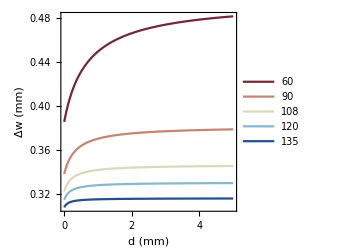
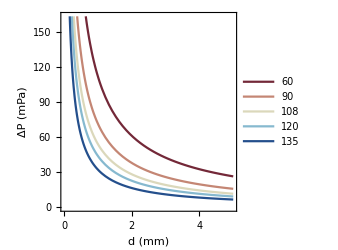

```mathematica
Clear[d];
is = 250;
tab = Table[wf[d, θ, 0.3], {θ, {60, 90, 108, 120, 135}*Degree}];
p1 = Plot[tab, {d, 0, 5}, PlotStyle->getColors[5], PlotLegends->{60, 90, 108, 120, 135}, FrameLabel->{"d (mm)", "Δw (mm)"}, ImageSize->is];
tab = Table[dp[d, θ, 0.3, 20], {θ, {60, 90, 108, 120, 135}*Degree}];
p2 = Plot[tab, {d, 0, 5}, PlotStyle->getColors[5], PlotLegends->{60, 90, 108, 120, 135}, FrameLabel->{"d (mm)", "ΔP (mPa)"}, ImageSize->is];
Row[{p1, p2}, "\t"]
```

The displaced length d is determined numerically

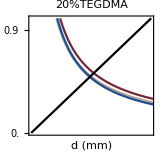
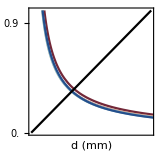
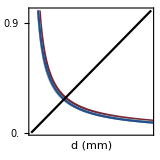
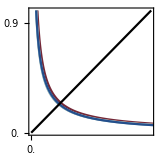
vs = 3 mm/s | -Graphics- | -Graphics- | -Graphics- | -Graphics-
vs = 6 mm/s | -Graphics- | -Graphics- | -Graphics- | -Graphics-
vs = 9 mm/s | -Graphics- | -Graphics- | -Graphics- | -Graphics-
vs = 12 mm/s | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
tick1 = 0.3;
tick2 = 0.1;
row2 = Grid[Table[
ticksx = {Join[{#,If[v==12,#,""], {0.02, 0}}&/@Range[0, 3, tick1], {#,"", {0.01, 0}}&/@Complement[Range[0, 3,tick2],Range[0, 3, tick1]]], Join[{#,"", {0.02, 0}}&/@Range[0, 3, tick1], {#,"", {0.01, 0}}&/@Complement[Range[0, 3, tick2],Range[0, 3,tick1]]]};
Prepend[
Table[
ticksy = {Join[{#,If[ink==20,#,""], {0.02, 0}}&/@Range[0, 3, tick1], {#,"", {0.01, 0}}&/@Complement[Range[0, 3,tick2],Range[0, 3, tick1]]], Join[{#,"", {0.02, 0}}&/@Range[0, 3, tick1], {#,"", {0.01, 0}}&/@Complement[Range[0, 3, tick2],Range[0, 3,tick1]]]};
tab = Append[Table[dinit[d, θ, ink, v, 0.05], {θ, {60, 90, 108, 120, 135}*Degree}],d];
Plot[ tab, {d, 0, 5}
, PlotStyle->Append[getColors[5], Black]
, FrameLabel->{"d (mm)",If[ink==20,  Row[{Subscript["d", "init"], "(d) (mm)"}], None]}
, PlotLegends->If[ink==35, Append[{60, 90, 108, 120, 135}, "d=d"], None]
, PlotRange->{{0, 1}, {0,1}}
, ImagePadding->{{If[ink==20, 40, 2], 2},{If[v==12,40,2],2}}
, PlotLabel->If[v==3,Style[(ToString[ink]<>"%TEGDMA"), 10], None]
, LabelStyle->Directive[10, Black]
, ImageSize->160-If[ink==20, 0, 38]
, FrameTicks->{ticksy, ticksx}]
,{ink, 20, 35, 5}],Rotate[Style[Text["vs = "<>ToString[v]<>" mm/s"], 10], Pi/2]], {v, 3, 12,3}]]
```

```mathematica
ink = 25;
laptable =Flatten[ Table[
s1 = Select[Solve[dinit[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
di = If[Length[s1]==1, s1[[1]], 0];
s1 = Select[Solve[drelax[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
dr = If[Length[s1]==1, s1[[1]], 0];
s1 = Select[Solve[dshear[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
ds = If[Length[s1]==1, s1[[1]], 0];
{θ/Degree, ink, vs, λ
, di, If[di>0,changewidth[di, θ],0], If[di>0,changepos[di, θ],0]
, dr, If[dr>0,changewidth[dr, θ],0], If[dr>0,changepos[dr, θ],0]
, ds, If[ds>0,changewidth[ds, θ],0], If[ds>0,changepos[ds, θ],0]}
, {λ, {0.0005, 0.001, 0.005, 0.01}}, {θ, {60, 90, 108, 120, 135}*Degree}, {vs, 3, 12, 3}],2];
Grid[Prepend[laptable, {"angle", "ink", "vs", "lambda", "dinit", "dwidth init", "dpos init", "drelax", "dwidth relax", "dpos relax", "dshear", "dwidth shear", "dpos shear"}]]
```

angle | ink | vs | lambda | dinit | dwidth init | dpos init | drelax | dwidth relax | dpos relax | dshear | dwidth shear | dpos shear
60 | 25 | 3 | 0.0005 | 0.0481137 | 0.09317 | 0.0655968 | 0.37751 | 0.124431 | 0.15287 | 0.385798 | 0.124962 | 0.15513
60 | 25 | 6 | 0.0005 | 0.033724 | 0.0910904 | 0.0619627 | 0.259409 | 0.115845 | 0.120924 | 0.265069 | 0.116306 | 0.122442
60 | 25 | 9 | 0.0005 | 0.0274246 | 0.0901499 | 0.0603793 | 0.208568 | 0.111429 | 0.107351 | 0.213095 | 0.111843 | 0.108554
60 | 25 | 12 | 0.0005 | 0.0236922 | 0.0895837 | 0.0594434 | 0.178795 | 0.10859 | 0.0994664 | 0.182659 | 0.10897 | 0.100487
90 | 25 | 3 | 0.0005 | 0.0441192 | 0.0434923 | 0.0414794 | 0.41997 | 0.0622063 | 0.144947 | 0.426862 | 0.0623789 | 0.146905
90 | 25 | 6 | 0.0005 | 0.030755 | 0.0421156 | 0.0380518 | 0.288017 | 0.0581828 | 0.107721 | 0.292766 | 0.0583563 | 0.109051
90 | 25 | 9 | 0.0005 | 0.0249436 | 0.0414841 | 0.036573 | 0.230878 | 0.0558707 | 0.0918034 | 0.234687 | 0.056039 | 0.0928595
90 | 25 | 12 | 0.0005 | 0.0215132 | 0.0411013 | 0.0357036 | 0.197368 | 0.0542874 | 0.0825481 | 0.20062 | 0.0544497 | 0.0834435
108 | 25 | 3 | 0.0005 | 0.0432226 | 0.0263631 | 0.0293451 | 0.469817 | 0.0386771 | 0.136501 | 0.475898 | 0.0387464 | 0.138071
108 | 25 | 6 | 0.0005 | 0.0300081 | 0.0253458 | 0.0262829 | 0.323384 | 0.0365602 | 0.098865 | 0.327614 | 0.0366366 | 0.099946
108 | 25 | 9 | 0.0005 | 0.0242875 | 0.0248725 | 0.0249707 | 0.259493 | 0.0352484 | 0.082601 | 0.262903 | 0.0353268 | 0.0834657
108 | 25 | 12 | 0.0005 | 0.0209196 | 0.0245837 | 0.0242022 | 0.221859 | 0.0343057 | 0.0730897 | 0.224781 | 0.0343844 | 0.073826
120 | 25 | 3 | 0.0005 | 0.0430831 | 0.018032 | 0.0222856 | 0.517274 | 0.026638 | 0.128596 | 0.522782 | 0.0266702 | 0.12986
120 | 25 | 6 | 0.0005 | 0.029817 | 0.0172377 | 0.0195511 | 0.357515 | 0.0254204 | 0.0920505 | 0.361369 | 0.0254581 | 0.0929285
120 | 25 | 9 | 0.0005 | 0.0240917 | 0.0168629 | 0.0183848 | 0.287451 | 0.0246274 | 0.0761353 | 0.29057 | 0.0246677 | 0.0768417
120 | 25 | 12 | 0.0005 | 0.0207279 | 0.0166327 | 0.0177039 | 0.246033 | 0.0240376 | 0.0667797 | 0.248714 | 0.0240792 | 0.0673838
135 | 25 | 3 | 0.0005 | 0.043455 | 0.0102182 | 0.0146836 | 0.602884 | 0.0149677 | 0.115297 | 0.607612 | 0.0149771 | 0.116161
135 | 25 | 6 | 0.0005 | 0.0299385 | 0.0096874 | 0.0124449 | 0.419331 | 0.0144774 | 0.0817913 | 0.422658 | 0.0144892 | 0.0823973
135 | 25 | 9 | 0.0005 | 0.024126 | 0.00942993 | 0.0114957 | 0.338407 | 0.0141392 | 0.0670759 | 0.341111 | 0.0141524 | 0.0675669
135 | 25 | 12 | 0.0005 | 0.0207199 | 0.00926962 | 0.0109438 | 0.290372 | 0.0138768 | 0.0583698 | 0.292705 | 0.0138909 | 0.058792
60 | 25 | 3 | 0.001 | 0.0688434 | 0.0960089 | 0.0708712 | 0.550237 | 0.134013 | 0.200337 | 0.562339 | 0.134585 | 0.203687
60 | 25 | 6 | 0.001 | 0.0481137 | 0.09317 | 0.0655968 | 0.37751 | 0.124431 | 0.15287 | 0.385798 | 0.124962 | 0.15513
60 | 25 | 9 | 0.001 | 0.0390711 | 0.0918741 | 0.0633103 | 0.303029 | 0.11926 | 0.132662 | 0.309661 | 0.119753 | 0.134453
60 | 25 | 12 | 0.001 | 0.033724 | 0.0910904 | 0.0619627 | 0.259409 | 0.115845 | 0.120924 | 0.265069 | 0.116306 | 0.122442
90 | 25 | 3 | 0.001 | 0.0635485 | 0.0453249 | 0.0465221 | 0.610754 | 0.0660744 | 0.199459 | 0.620684 | 0.0662344 | 0.202311
90 | 25 | 6 | 0.001 | 0.0441192 | 0.0434923 | 0.0414794 | 0.41997 | 0.0622063 | 0.144947 | 0.426862 | 0.0623789 | 0.146905
90 | 25 | 9 | 0.001 | 0.0357074 | 0.0426377 | 0.0393177 | 0.336895 | 0.0598536 | 0.121447 | 0.342442 | 0.0600283 | 0.12301
90 | 25 | 12 | 0.001 | 0.030755 | 0.0421156 | 0.0380518 | 0.288017 | 0.0581828 | 0.107721 | 0.292766 | 0.0583563 | 0.109051
108 | 25 | 3 | 0.001 | 0.0625357 | 0.0276845 | 0.0338873 | 0.67966 | 0.0405394 | 0.190908 | 0.688351 | 0.0405985 | 0.193169
108 | 25 | 6 | 0.001 | 0.0432226 | 0.0263631 | 0.0293451 | 0.469817 | 0.0386771 | 0.136501 | 0.475898 | 0.0387464 | 0.138071
108 | 25 | 9 | 0.001 | 0.0348964 | 0.025734 | 0.0274109 | 0.377788 | 0.0374635 | 0.1128 | 0.382709 | 0.0375374 | 0.114064
108 | 25 | 12 | 0.001 | 0.0300081 | 0.0253458 | 0.0262829 | 0.323384 | 0.0365602 | 0.098865 | 0.327614 | 0.0366366 | 0.099946
120 | 25 | 3 | 0.001 | 0.0625305 | 0.0190394 | 0.0263622 | 0.745065 | 0.0276524 | 0.181015 | 0.752903 | 0.0276786 | 0.182823
120 | 25 | 6 | 0.001 | 0.0430831 | 0.018032 | 0.0222856 | 0.517274 | 0.026638 | 0.128596 | 0.522782 | 0.0266702 | 0.12986
120 | 25 | 9 | 0.001 | 0.0347187 | 0.0175426 | 0.0205565 | 0.416981 | 0.0259489 | 0.105621 | 0.421454 | 0.0259844 | 0.106643
120 | 25 | 12 | 0.001 | 0.029817 | 0.0172377 | 0.0195511 | 0.357515 | 0.0254204 | 0.0920505 | 0.361369 | 0.0254581 | 0.0929285
135 | 25 | 3 | 0.001 | 0.063313 | 0.0108615 | 0.0180358 | 0.863416 | 0.0153525 | 0.162997 | 0.870121 | 0.0153598 | 0.164226
135 | 25 | 6 | 0.001 | 0.043455 | 0.0102182 | 0.0146836 | 0.602884 | 0.0149677 | 0.115297 | 0.607612 | 0.0149771 | 0.116161
135 | 25 | 9 | 0.001 | 0.0349268 | 0.00989361 | 0.0132663 | 0.487778 | 0.0146943 | 0.0942696 | 0.491628 | 0.0147051 | 0.0949723
135 | 25 | 12 | 0.001 | 0.0299385 | 0.0096874 | 0.0124449 | 0.419331 | 0.0144774 | 0.0817913 | 0.422658 | 0.0144892 | 0.0823973
60 | 25 | 3 | 0.005 | 0.160452 | 0.106735 | 0.0946346 | 1.31469 | 0.156799 | 0.415318 | 1.34321 | 0.157326 | 0.42342
60 | 25 | 6 | 0.005 | 0.111154 | 0.101297 | 0.0817631 | 0.904818 | 0.147232 | 0.29939 | 0.924614 | 0.147802 | 0.304963
60 | 25 | 9 | 0.005 | 0.0898448 | 0.098713 | 0.0762577 | 0.726294 | 0.141388 | 0.249316 | 0.742237 | 0.141968 | 0.253773
60 | 25 | 12 | 0.005 | 0.0773153 | 0.0971196 | 0.0730391 | 0.621214 | 0.137221 | 0.220024 | 0.634869 | 0.137799 | 0.223821
90 | 25 | 3 | 0.005 | 0.150726 | 0.0517241 | 0.0697934 | 1.43464 | 0.0733334 | 0.438204 | 1.45735 | 0.0734405 | 0.444816
90 | 25 | 6 | 0.005 | 0.103636 | 0.0485852 | 0.0571108 | 0.995987 | 0.0705633 | 0.310704 | 1.01193 | 0.0706949 | 0.315328
90 | 25 | 9 | 0.005 | 0.0833903 | 0.0470176 | 0.0517352 | 0.80292 | 0.0686848 | 0.25482 | 0.815867 | 0.06883 | 0.258561
90 | 25 | 12 | 0.005 | 0.0715364 | 0.0460265 | 0.0486137 | 0.68847 | 0.0672453 | 0.221807 | 0.699625 | 0.0673993 | 0.22502
108 | 25 | 3 | 0.005 | 0.149609 | 0.0319826 | 0.0550372 | 1.57578 | 0.043663 | 0.425203 | 1.59542 | 0.0436975 | 0.430352
108 | 25 | 6 | 0.005 | 0.102558 | 0.0299367 | 0.0434969 | 1.09988 | 0.0425217 | 0.300567 | 1.11372 | 0.0425662 | 0.304189
108 | 25 | 9 | 0.005 | 0.0823293 | 0.0288699 | 0.0386109 | 0.889681 | 0.0417135 | 0.245641 | 0.900957 | 0.0417644 | 0.248584
108 | 25 | 12 | 0.005 | 0.0704983 | 0.0281801 | 0.03578 | 0.764721 | 0.0410737 | 0.213052 | 0.774461 | 0.0411292 | 0.215589
120 | 25 | 3 | 0.005 | 0.150222 | 0.0221144 | 0.0453796 | 1.7129 | 0.0292523 | 0.40491 | 1.73053 | 0.0292665 | 0.408995
120 | 25 | 6 | 0.005 | 0.10288 | 0.0206892 | 0.0350108 | 1.19945 | 0.0286813 | 0.28601 | 1.21189 | 0.0287001 | 0.28889
120 | 25 | 9 | 0.005 | 0.0824875 | 0.0199184 | 0.0306125 | 0.97235 | 0.0282677 | 0.233491 | 0.982498 | 0.0282896 | 0.235836
120 | 25 | 12 | 0.005 | 0.0705578 | 0.0194097 | 0.0280645 | 0.837178 | 0.0279347 | 0.202268 | 0.845954 | 0.0279589 | 0.204294
135 | 25 | 3 | 0.005 | 0.152391 | 0.0126253 | 0.0335911 | 1.96598 | 0.0159222 | 0.365353 | 1.98101 | 0.0159258 | 0.368113
135 | 25 | 6 | 0.005 | 0.104434 | 0.0118436 | 0.0251389 | 1.3815 | 0.0157237 | 0.258034 | 1.39212 | 0.0157286 | 0.259983
135 | 25 | 9 | 0.005 | 0.0836762 | 0.0113955 | 0.0215313 | 1.12273 | 0.0155766 | 0.210547 | 1.13139 | 0.0155825 | 0.212137
135 | 25 | 12 | 0.005 | 0.0715081 | 0.0110895 | 0.0194365 | 0.968561 | 0.0154561 | 0.182272 | 0.976061 | 0.0154628 | 0.183647
60 | 25 | 3 | 0.01 | 0.232544 | 0.113575 | 0.113736 | 1.90349 | 0.165384 | 0.583144 | 1.94435 | 0.165842 | 0.594825
60 | 25 | 6 | 0.01 | 0.160452 | 0.106735 | 0.0946346 | 1.31469 | 0.156799 | 0.415318 | 1.34321 | 0.157326 | 0.42342
60 | 25 | 9 | 0.01 | 0.129381 | 0.10339 | 0.0865016 | 1.05698 | 0.151292 | 0.342301 | 1.08004 | 0.151848 | 0.348817
60 | 25 | 12 | 0.01 | 0.111154 | 0.101297 | 0.0817631 | 0.904818 | 0.147232 | 0.29939 | 0.924614 | 0.147802 | 0.304963
90 | 25 | 3 | 0.01 | 0.219791 | 0.0553678 | 0.0887339 | 2.0582 | 0.0755477 | 0.620056 | 2.09043 | 0.0756316 | 0.629467
90 | 25 | 6 | 0.01 | 0.150726 | 0.0517241 | 0.0697934 | 1.43464 | 0.0733334 | 0.438204 | 1.45735 | 0.0734405 | 0.444816
90 | 25 | 9 | 0.01 | 0.121017 | 0.0498193 | 0.0617652 | 1.15946 | 0.0717818 | 0.358155 | 1.17794 | 0.0719032 | 0.363522
90 | 25 | 12 | 0.01 | 0.103636 | 0.0485852 | 0.0571108 | 0.995987 | 0.0705633 | 0.310704 | 1.01193 | 0.0706949 | 0.315328
108 | 25 | 3 | 0.01 | 0.218409 | 0.0342115 | 0.0722208 | 2.25031 | 0.0445359 | 0.602161 | 2.27813 | 0.0445619 | 0.609465
108 | 25 | 6 | 0.01 | 0.149609 | 0.0319826 | 0.0550372 | 1.57578 | 0.043663 | 0.425203 | 1.59542 | 0.0436975 | 0.430352
108 | 25 | 9 | 0.01 | 0.119931 | 0.0307553 | 0.0477324 | 1.27744 | 0.0430308 | 0.347037 | 1.29346 | 0.043071 | 0.35123
108 | 25 | 12 | 0.01 | 0.102558 | 0.0299367 | 0.0434969 | 1.09988 | 0.0425217 | 0.300567 | 1.11372 | 0.0425662 | 0.304189
120 | 25 | 3 | 0.01 | 0.219168 | 0.0235905 | 0.0607393 | 2.43989 | 0.0296793 | 0.573423 | 2.46485 | 0.0296899 | 0.579209
120 | 25 | 6 | 0.01 | 0.150222 | 0.0221144 | 0.0453796 | 1.7129 | 0.0292523 | 0.40491 | 1.73053 | 0.0292665 | 0.408995
120 | 25 | 9 | 0.01 | 0.120377 | 0.0212678 | 0.0388206 | 1.39111 | 0.0289378 | 0.330375 | 1.4055 | 0.0289546 | 0.333705
120 | 25 | 12 | 0.01 | 0.10288 | 0.0206892 | 0.0350108 | 1.19945 | 0.0286813 | 0.28601 | 1.21189 | 0.0287001 | 0.28889
135 | 25 | 3 | 0.01 | 0.221728 | 0.0133772 | 0.0459859 | 2.79294 | 0.0160675 | 0.517257 | 2.81419 | 0.0160701 | 0.521162
135 | 25 | 6 | 0.01 | 0.152391 | 0.0126253 | 0.0335911 | 1.96598 | 0.0159222 | 0.365353 | 1.98101 | 0.0159258 | 0.368113
135 | 25 | 9 | 0.01 | 0.122196 | 0.012168 | 0.0282533 | 1.59975 | 0.0158135 | 0.2981 | 1.61201 | 0.0158179 | 0.300352
135 | 25 | 12 | 0.01 | 0.104434 | 0.0118436 | 0.0251389 | 1.3815 | 0.0157237 | 0.258034 | 1.39212 | 0.0157286 | 0.259983

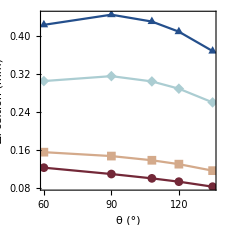
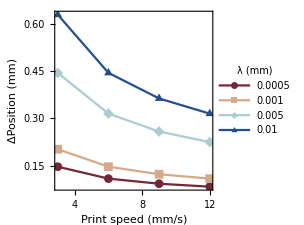
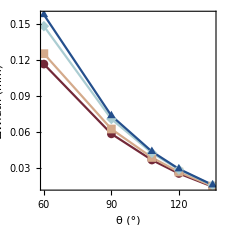
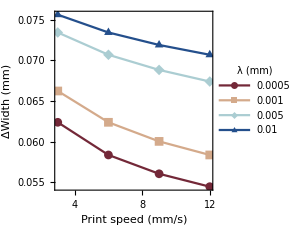

```mathematica
colors = getColors[4];
tp1 = GatherBy[laptable, #[[4]]&];
is = 225;
ip = {{70, 4}, {50, 2}};
c1 = Column[Table[
tp = Table[Select[tp1[[i]], #[[3]]==6&][[;;, {1, 12+j}]], {i, Length[tp1]}];
lambda2 = ListPlot[tp, PlotStyle->colors, PlotRange->All, Joined->True, FrameLabel->{"θ (°)", "Δ"<>Switch[j, 0, "Width", 1, "Position"]<>" (mm)"}, PlotRangePadding->Scaled[0.1],  ImageSize->is, LabelStyle->Directive[10*100/72, Black], ImagePadding->ip];
tp = Table[Select[tp1[[i]], #[[1]]==90&][[;;, {3, 12+j}]], {i, Length[tp1]}];
lambda3 = ListPlot[tp, PlotStyle->colors, PlotRange->All, Joined->True, FrameLabel->{"Print speed (mm/s)",  "Δ"<>Switch[j, 0, "Width", 1, "Position"]<>" (mm)"}, PlotRangePadding->Scaled[0.1], PlotLegends->PointLegend[colors, tp1[[;;, 1, 4]],LegendLabel->Row[{Style["λ", 10*100/72, Italic, FontFamily->"Times"], " (mm)"}]], ImageSize->is, LabelStyle->Directive[10*100/72, Black], ImagePadding->ip];
Row[{lambda2, lambda3}]
, {j, {1,0}}]]
```

Calculate and export the predicted changes in width and position as a function of printing parameters

```mathematica
λ = 0.001;
laptable = Flatten[Table[
s1 = Select[Solve[dinit[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
di = If[Length[s1]==1, s1[[1]], 0];
s1 = Select[Solve[drelax[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
dr = If[Length[s1]==1, s1[[1]], 0];
s1 = Select[Solve[dshear[d, θ, ink, vs, λ]==d, d][[;;,1,2]], Im[#]==0 && #>0&];
ds = If[Length[s1]==1, s1[[1]], 0];
{θ/Degree, ink, vs, λ
, di, If[di>0,changewidth[di, θ],0], If[di>0,changepos[di, θ],0]
, dr, If[dr>0,changewidth[dr, θ],0], If[dr>0,changepos[dr, θ],0]
, ds, If[ds>0,changewidth[ds, θ],0], If[ds>0,changepos[ds, θ],0]}
, {θ, {60, 90, 108, 120, 135}*Degree}, {ink, 20, 35, 5}, {vs, 3, 12, 3}],2];
Grid[Prepend[laptable, {"angle", "ink", "vs", "lambda", "dinit", "dwidth init", "dpos init", "drelax", "dwidth relax", "dpos relax", "dshear", "dwidth shear", "dpos shear"}]]
Export["Tables\\laptable.csv", laptable]
```

angle | ink | vs | lambda | dinit | dwidth init | dpos init | drelax | dwidth relax | dpos relax | dshear | dwidth shear | dpos shear
60 | 20 | 3 | 0.001 | 0.0647053 | 0.0954562 | 0.0698148 | 0.51562 | 0.132313 | 0.190769 | 0.526961 | 0.13288 | 0.193901
60 | 20 | 6 | 0.001 | 0.0452464 | 0.092763 | 0.0648708 | 0.353811 | 0.122867 | 0.14642 | 0.361573 | 0.123388 | 0.14853
60 | 20 | 9 | 0.001 | 0.0367525 | 0.0915359 | 0.0627256 | 0.284069 | 0.117815 | 0.12755 | 0.290279 | 0.118294 | 0.129223
60 | 20 | 12 | 0.001 | 0.0317281 | 0.0907945 | 0.0614605 | 0.243229 | 0.114494 | 0.116591 | 0.248528 | 0.114942 | 0.118009
60 | 25 | 3 | 0.001 | 0.0688434 | 0.0960089 | 0.0708712 | 0.550237 | 0.134013 | 0.200337 | 0.562339 | 0.134585 | 0.203687
60 | 25 | 6 | 0.001 | 0.0481137 | 0.09317 | 0.0655968 | 0.37751 | 0.124431 | 0.15287 | 0.385798 | 0.124962 | 0.15513
60 | 25 | 9 | 0.001 | 0.0390711 | 0.0918741 | 0.0633103 | 0.303029 | 0.11926 | 0.132662 | 0.309661 | 0.119753 | 0.134453
60 | 25 | 12 | 0.001 | 0.033724 | 0.0910904 | 0.0619627 | 0.259409 | 0.115845 | 0.120924 | 0.265069 | 0.116306 | 0.122442
60 | 30 | 3 | 0.001 | 0.0670805 | 0.0957742 | 0.0704209 | 0.535484 | 0.1333 | 0.196256 | 0.547262 | 0.133871 | 0.199513
60 | 30 | 6 | 0.001 | 0.0468924 | 0.0929971 | 0.0652874 | 0.367408 | 0.123773 | 0.150118 | 0.375472 | 0.1243 | 0.152315
60 | 30 | 9 | 0.001 | 0.0380837 | 0.0917304 | 0.0630612 | 0.294947 | 0.118651 | 0.130481 | 0.301399 | 0.119138 | 0.132222
60 | 30 | 12 | 0.001 | 0.032874 | 0.0909646 | 0.0617488 | 0.252512 | 0.115275 | 0.119075 | 0.258018 | 0.115731 | 0.120551
60 | 35 | 3 | 0.001 | 0.121312 | 0.102476 | 0.0844007 | 0.989696 | 0.149585 | 0.323304 | 1.01131 | 0.150147 | 0.329404
60 | 35 | 6 | 0.001 | 0.0843009 | 0.098015 | 0.0748318 | 0.679795 | 0.139622 | 0.236334 | 0.694728 | 0.140202 | 0.2405
60 | 35 | 9 | 0.001 | 0.0682568 | 0.0959309 | 0.0707213 | 0.545327 | 0.133778 | 0.198978 | 0.557321 | 0.134349 | 0.202297
60 | 35 | 12 | 0.001 | 0.0588048 | 0.0946562 | 0.0683114 | 0.466353 | 0.129718 | 0.177195 | 0.476609 | 0.130276 | 0.180016
90 | 20 | 3 | 0.001 | 0.0596559 | 0.0449725 | 0.0455066 | 0.572716 | 0.06543 | 0.188546 | 0.582045 | 0.0655929 | 0.19122
90 | 20 | 6 | 0.001 | 0.0414471 | 0.0432251 | 0.0407912 | 0.393591 | 0.0615162 | 0.137465 | 0.400058 | 0.0616898 | 0.139298
90 | 20 | 9 | 0.001 | 0.0335578 | 0.0424129 | 0.0387676 | 0.315669 | 0.0591582 | 0.115476 | 0.320871 | 0.0593327 | 0.116937
90 | 20 | 12 | 0.001 | 0.0289109 | 0.0419175 | 0.0375817 | 0.26985 | 0.0574942 | 0.102644 | 0.274301 | 0.0576667 | 0.103887
90 | 25 | 3 | 0.001 | 0.0635485 | 0.0453249 | 0.0465221 | 0.610754 | 0.0660744 | 0.199459 | 0.620684 | 0.0662344 | 0.202311
90 | 25 | 6 | 0.001 | 0.0441192 | 0.0434923 | 0.0414794 | 0.41997 | 0.0622063 | 0.144947 | 0.426862 | 0.0623789 | 0.146905
90 | 25 | 9 | 0.001 | 0.0357074 | 0.0426377 | 0.0393177 | 0.336895 | 0.0598536 | 0.121447 | 0.342442 | 0.0600283 | 0.12301
90 | 25 | 12 | 0.001 | 0.030755 | 0.0421156 | 0.0380518 | 0.288017 | 0.0581828 | 0.107721 | 0.292766 | 0.0583563 | 0.109051
90 | 30 | 3 | 0.001 | 0.0618894 | 0.0451755 | 0.046089 | 0.594554 | 0.0658063 | 0.194809 | 0.604228 | 0.0659675 | 0.197585
90 | 30 | 6 | 0.001 | 0.0429806 | 0.0433789 | 0.041186 | 0.408732 | 0.0619182 | 0.141757 | 0.415443 | 0.0620913 | 0.143662
90 | 30 | 9 | 0.001 | 0.0347915 | 0.0425423 | 0.0390832 | 0.32785 | 0.0595626 | 0.1189 | 0.33325 | 0.0597373 | 0.12042
90 | 30 | 12 | 0.001 | 0.0299694 | 0.0420315 | 0.0378514 | 0.280274 | 0.0578942 | 0.105556 | 0.284897 | 0.0580673 | 0.106849
90 | 35 | 3 | 0.001 | 0.113317 | 0.0492844 | 0.059699 | 1.08728 | 0.0712776 | 0.337191 | 1.10464 | 0.0714033 | 0.342231
90 | 35 | 6 | 0.001 | 0.07814 | 0.0465858 | 0.0503501 | 0.752359 | 0.0680854 | 0.240223 | 0.764515 | 0.0682344 | 0.243731
90 | 35 | 9 | 0.001 | 0.0629963 | 0.0452753 | 0.0463779 | 0.605365 | 0.0659862 | 0.197912 | 0.61521 | 0.0661466 | 0.200738
90 | 35 | 12 | 0.001 | 0.0541169 | 0.0444586 | 0.0440659 | 0.518415 | 0.0644132 | 0.173001 | 0.526882 | 0.0645799 | 0.175422
108 | 20 | 3 | 0.001 | 0.0586593 | 0.0274335 | 0.0329699 | 0.637952 | 0.0402398 | 0.180066 | 0.646126 | 0.0403007 | 0.18219
108 | 20 | 6 | 0.001 | 0.0405749 | 0.0261673 | 0.0287283 | 0.440649 | 0.0383279 | 0.128975 | 0.446363 | 0.0383986 | 0.130448
108 | 20 | 9 | 0.001 | 0.0327733 | 0.0255672 | 0.0269203 | 0.354188 | 0.0370919 | 0.106747 | 0.35881 | 0.037167 | 0.107932
108 | 20 | 12 | 0.001 | 0.0281909 | 0.0251978 | 0.0258652 | 0.303106 | 0.0361773 | 0.0936896 | 0.307077 | 0.0362545 | 0.0947022
108 | 25 | 3 | 0.001 | 0.0625357 | 0.0276845 | 0.0338873 | 0.67966 | 0.0405394 | 0.190908 | 0.688351 | 0.0405985 | 0.193169
108 | 25 | 6 | 0.001 | 0.0432226 | 0.0263631 | 0.0293451 | 0.469817 | 0.0386771 | 0.136501 | 0.475898 | 0.0387464 | 0.138071
108 | 25 | 9 | 0.001 | 0.0348964 | 0.025734 | 0.0274109 | 0.377788 | 0.0374635 | 0.1128 | 0.382709 | 0.0375374 | 0.114064
108 | 25 | 12 | 0.001 | 0.0300081 | 0.0253458 | 0.0262829 | 0.323384 | 0.0365602 | 0.098865 | 0.327614 | 0.0366366 | 0.099946
108 | 30 | 3 | 0.001 | 0.0608831 | 0.0275783 | 0.0334959 | 0.661904 | 0.0404152 | 0.186291 | 0.670375 | 0.0404751 | 0.188493
108 | 30 | 6 | 0.001 | 0.0420941 | 0.0262801 | 0.029082 | 0.457396 | 0.038532 | 0.133295 | 0.463321 | 0.0386019 | 0.134824
108 | 30 | 9 | 0.001 | 0.0339916 | 0.0256632 | 0.0272017 | 0.367736 | 0.0373087 | 0.110221 | 0.37253 | 0.0373832 | 0.111451
108 | 30 | 12 | 0.001 | 0.0292338 | 0.025283 | 0.0261048 | 0.314746 | 0.0364005 | 0.096659 | 0.318866 | 0.0364772 | 0.0977109
108 | 35 | 3 | 0.001 | 0.112234 | 0.0304028 | 0.0458518 | 1.19908 | 0.0428216 | 0.326522 | 1.21414 | 0.0428635 | 0.330464
108 | 35 | 6 | 0.001 | 0.0770873 | 0.0285708 | 0.0373539 | 0.834516 | 0.0414493 | 0.231246 | 0.845114 | 0.0415021 | 0.234011
108 | 35 | 9 | 0.001 | 0.0619856 | 0.0276493 | 0.033757 | 0.673754 | 0.0404986 | 0.189372 | 0.682372 | 0.0405579 | 0.191613
108 | 35 | 12 | 0.001 | 0.0531488 | 0.0270648 | 0.0316705 | 0.578311 | 0.0397586 | 0.164583 | 0.585746 | 0.0398224 | 0.166511
120 | 20 | 3 | 0.001 | 0.0586239 | 0.0188502 | 0.0255376 | 0.69986 | 0.0274925 | 0.170595 | 0.707237 | 0.0275197 | 0.172295
120 | 20 | 6 | 0.001 | 0.0404214 | 0.0178803 | 0.0217336 | 0.485521 | 0.026442 | 0.121312 | 0.490702 | 0.0264752 | 0.1225
120 | 20 | 9 | 0.001 | 0.0325888 | 0.0174119 | 0.0201189 | 0.391205 | 0.0257331 | 0.0997328 | 0.395409 | 0.0257696 | 0.100693
120 | 20 | 12 | 0.001 | 0.0279969 | 0.0171208 | 0.0191794 | 0.335308 | 0.0251921 | 0.0869962 | 0.33893 | 0.0252307 | 0.0878199
120 | 25 | 3 | 0.001 | 0.0625305 | 0.0190394 | 0.0263622 | 0.745065 | 0.0276524 | 0.181015 | 0.752903 | 0.0276786 | 0.182823
120 | 25 | 6 | 0.001 | 0.0430831 | 0.018032 | 0.0222856 | 0.517274 | 0.026638 | 0.128596 | 0.522782 | 0.0266702 | 0.12986
120 | 25 | 9 | 0.001 | 0.0347187 | 0.0175426 | 0.0205565 | 0.416981 | 0.0259489 | 0.105621 | 0.421454 | 0.0259844 | 0.106643
120 | 25 | 12 | 0.001 | 0.029817 | 0.0172377 | 0.0195511 | 0.357515 | 0.0254204 | 0.0920505 | 0.361369 | 0.0254581 | 0.0929285
120 | 30 | 3 | 0.001 | 0.0608649 | 0.0189594 | 0.0260103 | 0.725823 | 0.0275863 | 0.176579 | 0.733465 | 0.0276129 | 0.178341
120 | 30 | 6 | 0.001 | 0.0419484 | 0.0179678 | 0.0220501 | 0.503756 | 0.0265567 | 0.125494 | 0.509125 | 0.0265894 | 0.126725
120 | 30 | 9 | 0.001 | 0.0338108 | 0.0174872 | 0.0203698 | 0.406006 | 0.0258593 | 0.103113 | 0.410364 | 0.0258953 | 0.104109
120 | 30 | 12 | 0.001 | 0.0290412 | 0.0171881 | 0.0193926 | 0.348058 | 0.0253255 | 0.0898972 | 0.351814 | 0.0253636 | 0.0907521
120 | 35 | 3 | 0.001 | 0.112627 | 0.02102 | 0.0371295 | 1.30654 | 0.0288327 | 0.310795 | 1.32007 | 0.0288503 | 0.313927
120 | 35 | 6 | 0.001 | 0.0772017 | 0.0196988 | 0.0294811 | 0.912696 | 0.0281308 | 0.219707 | 0.922238 | 0.0281537 | 0.221911
120 | 35 | 9 | 0.001 | 0.0619761 | 0.0190129 | 0.026245 | 0.738665 | 0.0276307 | 0.17954 | 0.746438 | 0.0276571 | 0.181332
120 | 35 | 12 | 0.001 | 0.0530727 | 0.0185704 | 0.0243705 | 0.635167 | 0.0272331 | 0.155695 | 0.641883 | 0.0272619 | 0.157241
135 | 20 | 3 | 0.001 | 0.0593234 | 0.0107432 | 0.0173573 | 0.811782 | 0.0152931 | 0.153536 | 0.818095 | 0.0153007 | 0.154692
135 | 20 | 6 | 0.001 | 0.0407395 | 0.0101184 | 0.0142307 | 0.566477 | 0.014891 | 0.108641 | 0.570928 | 0.0149008 | 0.109455
135 | 20 | 9 | 0.001 | 0.0327582 | 0.00980555 | 0.0129085 | 0.45813 | 0.0146065 | 0.0888619 | 0.461755 | 0.0146177 | 0.0895227
135 | 20 | 12 | 0.001 | 0.0280888 | 0.00960756 | 0.0121419 | 0.39372 | 0.0143817 | 0.0771289 | 0.39685 | 0.0143939 | 0.0776986
135 | 25 | 3 | 0.001 | 0.063313 | 0.0108615 | 0.0180358 | 0.863416 | 0.0153525 | 0.162997 | 0.870121 | 0.0153598 | 0.164226
135 | 25 | 6 | 0.001 | 0.043455 | 0.0102182 | 0.0146836 | 0.602884 | 0.0149677 | 0.115297 | 0.607612 | 0.0149771 | 0.116161
135 | 25 | 9 | 0.001 | 0.0349268 | 0.00989361 | 0.0132663 | 0.487778 | 0.0146943 | 0.0942696 | 0.491628 | 0.0147051 | 0.0949723
135 | 25 | 12 | 0.001 | 0.0299385 | 0.0096874 | 0.0124449 | 0.419331 | 0.0144774 | 0.0817913 | 0.422658 | 0.0144892 | 0.0823973
135 | 30 | 3 | 0.001 | 0.0616121 | 0.0108117 | 0.0177462 | 0.841441 | 0.015328 | 0.15897 | 0.847979 | 0.0153354 | 0.160168
135 | 30 | 6 | 0.001 | 0.0422972 | 0.0101761 | 0.0144904 | 0.587388 | 0.014936 | 0.112463 | 0.591998 | 0.0149455 | 0.113306
135 | 30 | 9 | 0.001 | 0.0340022 | 0.00985635 | 0.0131137 | 0.475158 | 0.014658 | 0.0919673 | 0.478912 | 0.0146689 | 0.0926521
135 | 30 | 12 | 0.001 | 0.02915 | 0.0096536 | 0.0123156 | 0.408429 | 0.0144378 | 0.0798061 | 0.411672 | 0.0144497 | 0.0803966
135 | 35 | 3 | 0.001 | 0.114335 | 0.0120303 | 0.0268722 | 1.50346 | 0.0157768 | 0.280422 | 1.515 | 0.0157814 | 0.282541
135 | 35 | 6 | 0.001 | 0.0782867 | 0.0112644 | 0.0206014 | 1.05471 | 0.0155273 | 0.19807 | 1.06286 | 0.0155335 | 0.199565
135 | 35 | 9 | 0.001 | 0.0627468 | 0.010845 | 0.0179394 | 0.856108 | 0.0153445 | 0.161658 | 0.862757 | 0.0153518 | 0.162876
135 | 35 | 12 | 0.001 | 0.0536539 | 0.0105662 | 0.0163972 | 0.737836 | 0.0151958 | 0.139991 | 0.743589 | 0.015204 | 0.141045

Tables\laptable.csv

Model the replaced arc

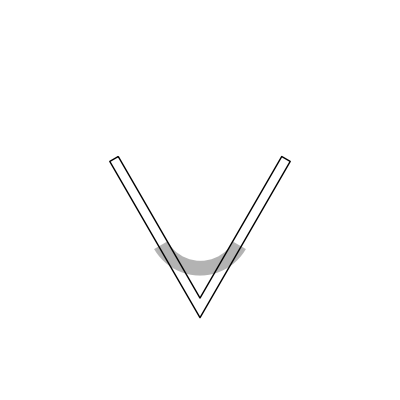

```mathematica
(*Manipulate[*)
θ=60*Degree;
d = 2;
r1 = d*Tan[θ/2];
ainit = 2*0.3*(d+0.3*Cot[θ/2]/2);
dd = (-(Pi-θ)*d*Tan[θ/2]+Sqrt[(Pi-θ)^2(d^2Tan[θ/2]^2)-2(Pi-θ)(-ainit)])/(Pi-θ);
r2 = r1+dd;
cent = {0, d*Sec[θ/2]};
(*Row[{*)
Graphics[{
GrayLevel[0.7]
,Disk[cent, r2, { Pi+θ/2, 2*Pi-θ/2}]
, White
, Disk[cent, r1]
,Black
,Line[{
5{-Cos[(Pi-θ)/2],Sin[(Pi-θ)/2]}
, {0,0}
, 5{Sin[θ/2],Cos[θ/2]}
, 5{Sin[θ/2],Cos[θ/2]}+0.3{Cos[θ/2], -Sin[θ/2]}
, {0, -0.3Csc[θ/2]}
, 5{-Sin[θ/2],Cos[θ/2]}+0.3*{-Cos[θ/2], -Sin[θ/2]}
, 5{-Sin[θ/2],Cos[θ/2]}
} ]
(*,Line[{d* {Sin[θ/2],Cos[θ/2]},  d{Sin[θ/2],Cos[θ/2]}+dd{Cos[θ/2], -Sin[θ/2]}}]
,Line[{d*{-Sin[θ/2],Cos[θ/2]},  d{-Sin[θ/2],Cos[θ/2]}+dd*{-Cos[θ/2], -Sin[θ/2]}}]*)
}
, Axes->False, PlotRange->{{-5, 5}, {-2,8}}, AspectRatio->1, Ticks->{Range[-6, 6, 0.6], Range[-1.8,10,0.6]}, ImageSize->400]
(*,
Grid[{{"A init", ainit}, {"A final", (Pi-θ)/(2*Pi)*Pi*(r2^2 - r1^2)}, {"r1", r1}, {"r2", r2}, {"dd", dd}}]
}]*)
(*,{d, 0.3, 5}, {θ, {60, 90, 108, 120, 135}*Degree}]*)
```

## Huang model

capillary bulge formation model
see: K.-M. Huang, T.-Y. Tsou, C.-W. Chang and Y.-C. Liao, Langmuir, 2017, 33, 645–651.

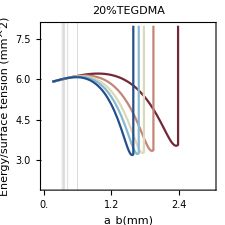
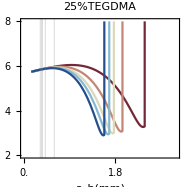
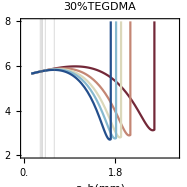
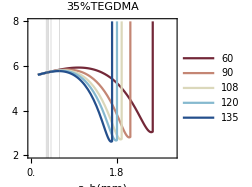

```mathematica
r = Row[Table[
Plot[{energyink[ab,60, ink], energyink[ab, 90, ink], energyink[ab, 108, ink], energyink[ab, 120, ink], energyink[ab, 135, ink]}
, {ab, 0.15, 3}
, PlotRange->{{0, 3}, {2, 8}}
, ImagePadding->{{If[ink==20, 40, 2], 2},{40,2}}
, PlotStyle->getColors[5]
, PlotLegends->If[ink==35, {60, 90, 108, 120, 135}, None]
, PlotLabel->Style[(ToString[ink]<>"%TEGDMA"), 10]
,FrameLabel->{Row[{Subscript["a", "b"],"(mm)"}],If[ink==20, "Energy/surface tension (mm^2)", None]}
, LabelStyle->Directive[10, Black]
, ImageSize->225-If[ink==20, 0, 38]
,GridLines->{Table[0.3/Sin[t*Degree/2], {t, {60, 90, 108, 120, 135}}], None}
, FrameTicks->{{Automatic, Automatic}, {Join[{#,#, {0.02, 0}}&/@Range[0, 3, 0.6], {#,"", {0.01, 0}}&/@Range[0, 3, 0.1]], Join[{#,"", {0.02, 0}}&/@Range[0, 3, 0.6], {#,"", {0.01, 0}}&/@Range[0, 3, 0.1]]}}
]
,{ink, 20, 35, 5}]];
r
```

## experimental data

### as a function of distance

```mathematica
(*cf2d and cf3d are lists of all the frames collected for all experiments*)
cf2d = Flatten[Import/@FileNames["*gras_D2_u*_*v_*_*_32_16_3_2_combined.csv", "32_16_3_2_combined", Infinity],1];
cf3d = Flatten[Import/@FileNames["*gras_D3_u*_*v_*_*_32_16_3_2_combined.csv", "32_16_3_2_combined", Infinity],1];
```

```mathematica
cf2db = removestartcorners[cf2d]; (*remove corners at the beginning of the edge, layerbylayer*)
cf3db = removestartcorners[cf3d]; (*remove corners at the beginning of the edge, bath*)
cf2df = removeendcorners[cf2d];(*remove corners at the end of the edge, layerbylayer*)
cf3df = removeendcorners[cf3d];(*remove corners at the end of the edge, bath*)
Grid[Dimensions/@{cf2d, cf3d, cf2db, cf3db, cf2df, cf3df}]
```

204672 | 59
204549 | 59
164837 | 59
165494 | 59
165953 | 59
165270 | 59

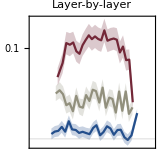
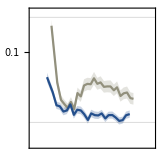
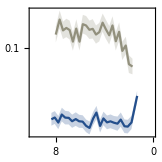
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[Table[distplotinitrow2[If[j==54, {cf2df, cf3df}, {cf2db, cf3db}], j==45, j==48, j, 10], {j, {45, 54, 48}}]]
```

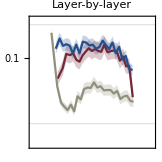
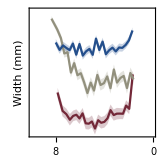
-Graphics--Graphics-
-Graphics--Graphics-

figures\timeplotsmaster.pdf

```mathematica
fig = Column[Table[distplotinitrow3[{cf2db, cf3db, cf2df, cf3df},p, !p, 10, p], {p, {True, False}}]]
Export["figures\\timeplotsmaster.pdf", fig]
```

```mathematica
tpspos = dpir3tps[True, cf2df, cf3df, cf2db, cf3db, 10];
tpsw = dpir3tps[False, cf2df, cf3df, cf2db, cf3db, 10];
```

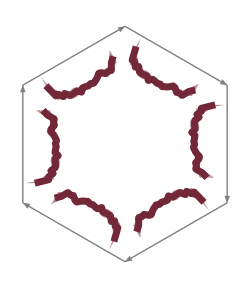
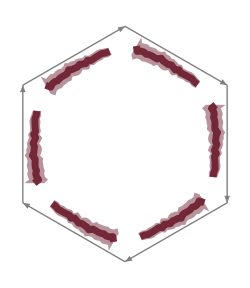
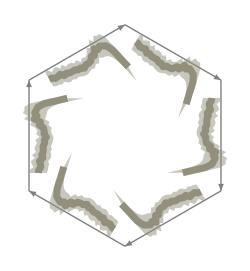
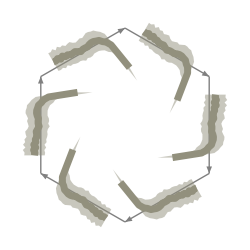
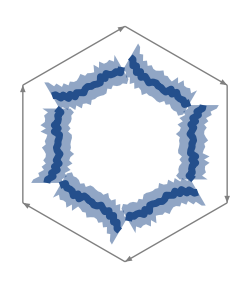
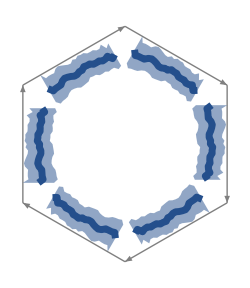

```mathematica
Table[wholepoly[j,i, tpspos, tpsw], {i, 3}, {j,2}]
```

### as a function of printing parameters

find differences between middle and corner

```mathematica
ctables = Prepend[Flatten[Table[
ct = changetable[{cf2db, cf3db, cf2df, cf3df}, i, j];
ct[[1]] = {j,i, 2, #[[1,1]], #[[1,2]], #[[2,1]]}&/@ct[[1]];
ct[[2]] = {j,i, 3, #[[1,1]], #[[1,2]], #[[2,1]]}&/@ct[[2]];
Flatten[ct,1]
,{i, 6}, {j, {1,2,6}}],2], {"split var", "plot mode", "support mode", "y", "ster"}]
Export["Tables\\cornerchanges.csv", ctables];
```

{{split var,plot mode,support mode,y,ster},{1,1,2,820,-0.0756685,0.0196608},{1,1,2,825,-0.0367775,0.0200607},{1,1,2,830,-0.0528426,0.0176139},{1,1,2,835,-0.0285407,0.0156555},{1,1,3,820,0.0176344,0.00624349},{1,1,3,825,0.000708652,0.00643456},{1,1,3,830,0.00363537,0.00543361},{1,1,3,835,0.00487219,0.00783013},{2,1,2,3,-0.0451526,0.0172269},{2,1,2,6,-0.0481309,0.0180106},{2,1,2,9,-0.0410438,0.0203022},{2,1,2,12,-0.0598701,0.0178203},{2,1,3,3,0.00812918,0.00547947},{2,1,3,6,0.000164893,0.00767099},{2,1,3,9,0.00750217,0.00619042},{2,1,3,12,0.0109869,0.00700399},{6,1,2,60,-0.103559,0.0270406},{6,1,2,90,-0.0606964,0.0255285},{6,1,2,108,-0.0301931,0.0233785},{6,1,2,120,-0.062245,0.0180341},{6,1,2,135,-0.0159059,0.0148237},{6,1,3,60,-0.006551,0.0105223},{6,1,3,90,0.0192666,0.00861045},{6,1,3,108,-0.00390967,0.0069752},{6,1,3,120,0.00339328,0.00639387},{6,1,3,135,0.0147109,0.00613304},{1,2,2,820,0.0232432,0.0165903},{1,2,2,825,0.0385896,0.0131085},{1,2,2,830,0.0707342,0.013474},{1,2,2,835,-0.0395186,0.0165815},{1,2,3,820,0.0817748,0.0109577},{1,2,3,825,0.0770309,0.0123333},{1,2,3,830,0.104337,0.010272},{1,2,3,835,0.065226,0.0117783},{2,2,2,3,0.00626468,0.0142054},{2,2,2,6,0.0156097,0.0150889},{2,2,2,9,0.0312075,0.0161817},{2,2,2,12,0.0391811,0.0152763},{2,2,3,3,0.0553966,0.00935176},{2,2,3,6,0.0562305,0.0101471},{2,2,3,9,0.104792,0.0123394},{2,2,3,12,0.112019,0.0128642},{6,2,2,60,0.0769179,0.032353},{6,2,2,90,0.0787156,0.022162},{6,2,2,108,0.0132535,0.0193682},{6,2,2,120,0.0244641,0.0146273},{6,2,2,135,0.00460517,0.0115804},{6,2,3,60,0.0459366,0.0245283},{6,2,3,90,0.152927,0.0165095},{6,2,3,108,0.137049,0.0146699},{6,2,3,120,0.0691764,0.0108588},{6,2,3,135,0.0420524,0.00859494},{1,3,2,820,-0.0467519,0.0155723},{1,3,2,825,-0.0190104,0.0150287},{1,3,2,830,-0.0287813,0.0127737},{1,3,2,835,-0.0576353,0.0149848},{1,3,3,820,0.0154682,0.00880316},{1,3,3,825,-0.0169895,0.0100852},{1,3,3,830,0.0258975,0.00771211},{1,3,3,835,0.00385689,0.0113152},{2,3,2,3,-0.0339456,0.0141519},{2,3,2,6,-0.0394736,0.0148575},{2,3,2,9,-0.0413956,0.0151392},{2,3,2,12,-0.0356235,0.014749},{2,3,3,3,0.0133701,0.00936551},{2,3,3,6,-0.00902276,0.00923703},{2,3,3,9,0.00812745,0.00949739},{2,3,3,12,0.0157679,0.0103135},{6,3,2,60,-0.0582098,0.0210152},{6,3,2,90,-0.0593312,0.0182601},{6,3,2,108,-0.0363154,0.016352},{6,3,2,120,-0.0187743,0.0153031},{6,3,2,135,-0.0343764,0.0136677},{6,3,3,60,0.00655176,0.0133969},{6,3,3,90,0.0364436,0.0126978},{6,3,3,108,-0.00707156,0.0102841},{6,3,3,120,0.0105725,0.0102035},{6,3,3,135,-0.00243145,0.00876379},{1,4,2,820,0.00416891,0.000950616},{1,4,2,825,0.00384956,0.00103005},{1,4,2,830,0.00429659,0.00102693},{1,4,2,835,0.00337464,0.000927226},{1,4,3,820,0.00185901,0.000523072},{1,4,3,825,0.00145815,0.000582384},{1,4,3,830,0.00324349,0.000596554},{1,4,3,835,0.00202458,0.000627822},{2,4,2,3,0.0021805,0.000894305},{2,4,2,6,0.0036515,0.000964899},{2,4,2,9,0.00539825,0.00105317},{2,4,2,12,0.0044435,0.00105728},{2,4,3,3,0.00245756,0.000608653},{2,4,3,6,0.00276536,0.000655611},{2,4,3,9,0.00166247,0.000678705},{2,4,3,12,0.00165848,0.000638821},{6,4,2,60,0.00568621,0.00137244},{6,4,2,90,0.00549317,0.00127392},{6,4,2,108,0.0031439,0.0011987},{6,4,2,120,0.0042605,0.000982788},{6,4,2,135,0.0024294,0.000876727},{6,4,3,60,0.00324826,0.000843198},{6,4,3,90,0.00245064,0.000722516},{6,4,3,108,0.00214074,0.00078862},{6,4,3,120,0.00214274,0.000655351},{6,4,3,135,0.00147058,0.000622933},{1,5,2,820,0.00849682,0.00101321},{1,5,2,825,0.00489668,0.000696277},{1,5,2,830,0.00447854,0.000878173},{1,5,2,835,0.00787639,0.000898237},{1,5,3,820,0.00201589,0.000544441},{1,5,3,825,0.00396141,0.00064424},{1,5,3,830,0.00377682,0.000594445},{1,5,3,835,0.00102445,0.000608612},{2,5,2,3,0.00549996,0.000843149},{2,5,2,6,0.00580368,0.000848047},{2,5,2,9,0.00697957,0.000968671},{2,5,2,12,0.00741785,0.000926924},{2,5,3,3,0.00243944,0.000608038},{2,5,3,6,0.00268744,0.000606679},{2,5,3,9,0.00385818,0.000624796},{2,5,3,12,0.00189511,0.00063933},{6,5,2,60,0.00416346,0.0013518},{6,5,2,90,0.0114998,0.00131785},{6,5,2,108,0.00650363,0.000951864},{6,5,2,120,0.00637087,0.000905123},{6,5,2,135,0.00440981,0.000735399},{6,5,3,60,0.00256827,0.00105023},{6,5,3,90,0.00162218,0.000836788},{6,5,3,108,0.00174094,0.000737051},{6,5,3,120,0.00384138,0.000574431},{6,5,3,135,0.00300934,0.000565206},{1,6,2,820,0.00159973,0.000735018},{1,6,2,825,0.00136409,0.000676769},{1,6,2,830,0.00151385,0.000620362},{1,6,2,835,0.00237537,0.000732434},{1,6,3,820,0.00176629,0.000496889},{1,6,3,825,0.00158329,0.000471959},{1,6,3,830,0.00275142,0.000694422},{1,6,3,835,0.00189056,0.000643931},{2,6,2,3,0.00221471,0.00074565},{2,6,2,6,0.00162394,0.000629277},{2,6,2,9,0.00250579,0.000667451},{2,6,2,12,0.00054186,0.00073721},{2,6,3,3,0.00306485,0.000627458},{2,6,3,6,0.00202999,0.000599396},{2,6,3,9,0.00184872,0.000637905},{2,6,3,12,0.0011899,0.000646035},{6,6,2,60,0.00271641,0.00104511},{6,6,2,90,0.00484766,0.000920755},{6,6,2,108,0.000713251,0.00077592},{6,6,2,120,0.000723988,0.000731975},{6,6,2,135,0.00113566,0.000609187},{6,6,3,60,0.00217759,0.000745102},{6,6,3,90,0.00130012,0.000753112},{6,6,3,108,0.00242258,0.000754666},{6,6,3,120,0.00193051,0.000594403},{6,6,3,135,0.00205387,0.000644175}}

```mathematica
ctables = Import["Tables\\cornerchanges.csv"];
```

plot changes as a function of independent variables

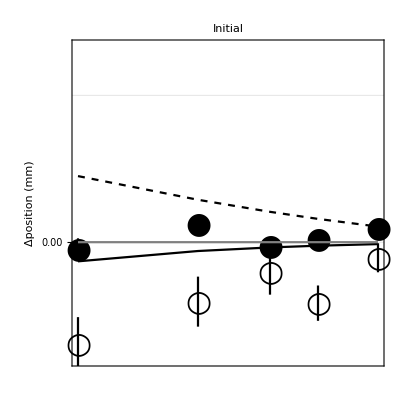
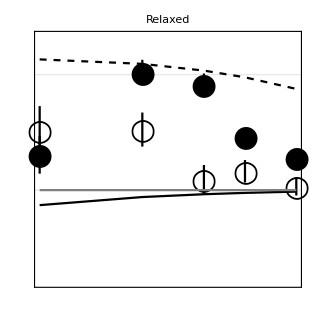
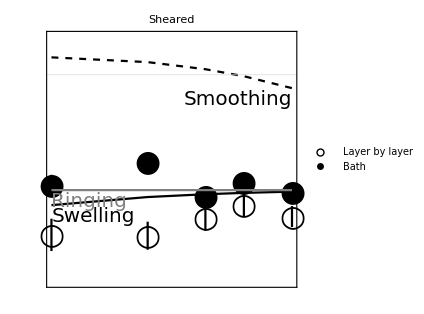
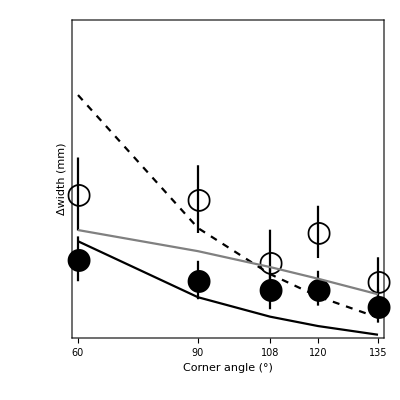
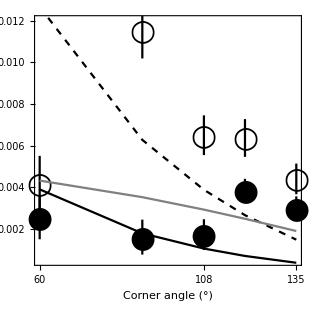
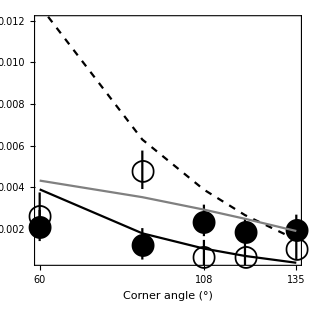
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

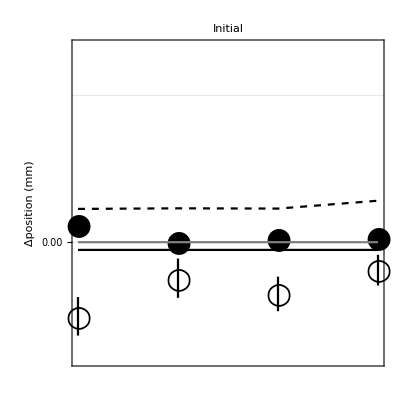
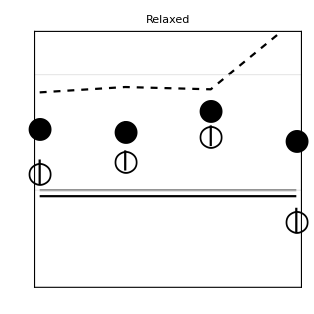
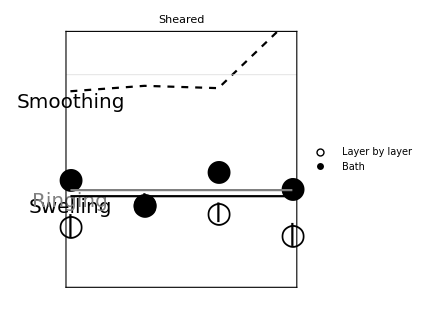
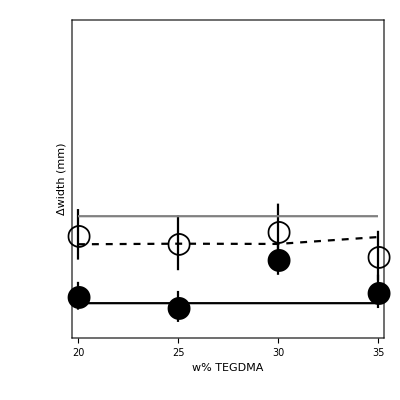
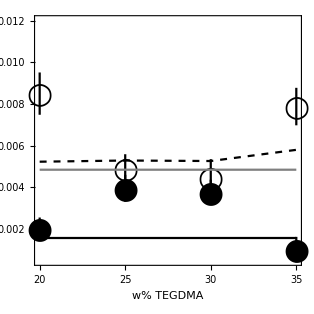
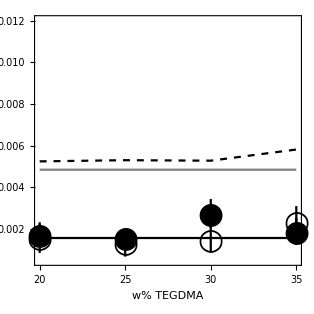
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

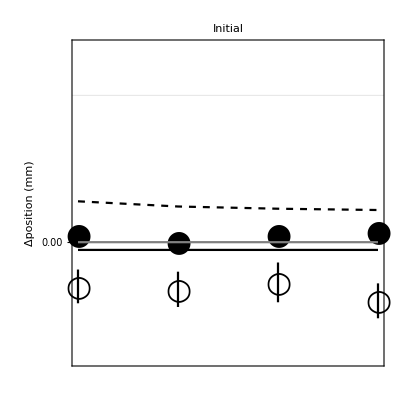
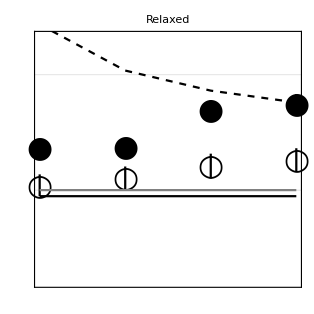
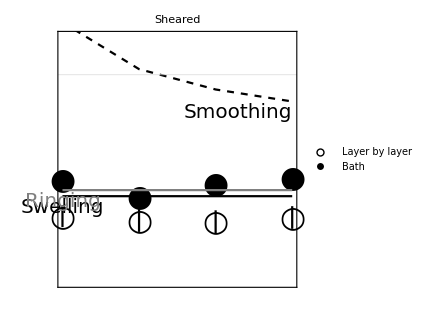
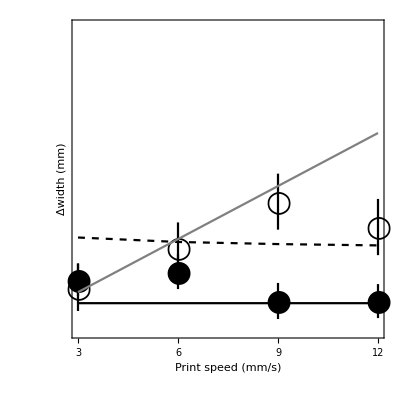
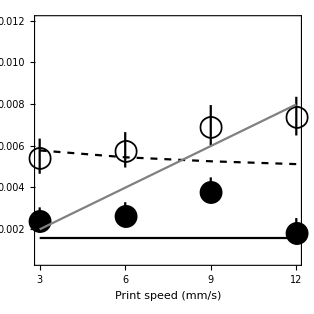
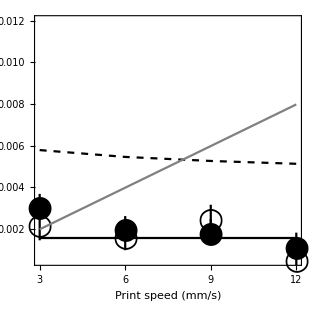
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
grid1 = plotgrid[ctables,6]
grid2 = plotgrid[ctables, 1]
grid3 = plotgrid[ctables, 2]
Export["figures\\timeplots_theorygridangle.pdf", grid1];
Export["figures\\timeplots_theorygridteg.pdf", grid2];
Export["figures\\timeplots_theorygridv.pdf", grid3];
```